## Data from Devon’s simulations

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
RhoTest937=Import["rho_test_937.dat"];   (* Importing the density profile of halo 937 --- the 1st column is distance in kpc and the second column is density in GeV cm^-3  *)
RhoTest937Table=ParallelTable[{RhoTest937[[i]][[1]],RhoTest937[[i]][[2]]},{i,3,101}];   (* Making a table of the density vs distance *)
RhoTest937TableLog=Log[10,RhoTest937Table];   
RhoTest937TableLogInterpolation=Interpolation[RhoTest937TableLog,InterpolationOrder->1]   (* Making an interpolation of the table of density [GeV cm^-3] versus distance [kpc] in Subscript[log, 10] basis *)
```

InterpolatingFunction[{{-1.97401,2.97548}},<>]

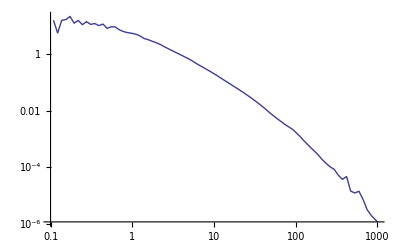

```mathematica
LogLogPlot[10^RhoTest937TableLogInterpolation[Log[10,radius]],{radius,0.1,10^3}]   (* Plotting the  interpolation of the table of density [GeV cm^-3] versus distance [kpc] *)
```

```mathematica
4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.108,193}]  (10^3 3.1 10^18)^3 1.783 10^-24 1/(2 10^33)  (* Mass of the halo in M_⊙ --- the factor (10^3 3.1 10^18)^3 converts kpc^3 to cm^3 --- the factor 1.783 * 10^-24 converts GeV to grams --- the factor 1/(2 10^33) converts grams to M_⊙ --- we integrate upto Subscript[R, 200] = 193 kpc *)
```

1.03759×10^12

```mathematica
GN=6.67 10^-11;   (* Subscript[G, N] in SI units of m^3 kg^-1 s^-2 -- value from PDG *)
mBH=2.6 10^6;   (* Mass of BH in MW in M_⊙ as given in Klypin, Zhao and Somerville *)
Mb=4.8 10^10;   (* Subscript[M, b]^vir in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rd=3.5;   (* rd in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
MassBaryon[r_]:=mBH+0.025 Mb (1-Exp[-2.64 r^1.15])+0.142 Mb(1-(1+r^1.5)Exp[-r^1.5])+0.833 Mb(1-(1+r/rd)Exp[-r/rd]);   (* Baryonic mass in M_⊙ inside radius r from eqn. 11 in Klypin, Zhao and Somerville *)
Mass[radius1_]:=MassBaryon[radius1]+4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.11,radius1}]  (10^3 3.1 10^18)^3 1.783 10^-24 1/(2 10^33);
   (* Mass at any radius radius1 --- here mass is in M_⊙ and radius1 is in kpc *)RadialVelocityDispersion[radius_]:=Sqrt[GN/10^RhoTest937TableLogInterpolation[Log[10,radius]] NIntegrate[10^RhoTest937TableLogInterpolation[Log[10,radiusprime]] 1/radiusprime^2 Mass[radiusprime](2 10^30),{radiusprime,radius,193.}](10^3 3.1 10^16)^-1] ;   (* Calculating Subscript[σ, v,r](r) as per eqn. 3 in DMVS paper --- here Mass is in M_⊙ so we multiply by 2*10^30 to convert it to kg --- we also multiply by the factor (10^3 3.1 10^16)^-1 to convert kpc^-1 to m^-1 *)
RadialVelocityDispersionNoBaryon[radius_]:=Sqrt[GN/10^RhoTest937TableLogInterpolation[Log[10,radius]] NIntegrate[10^RhoTest937TableLogInterpolation[Log[10,radiusprime]] 1/radiusprime^2(4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.11,radiusprime}]  (10^3 3.1 10^18)^3 1.783 10^-24 1/(2 10^33))(2 10^30),{radiusprime,radius,193.}](10^3 3.1 10^16)^-1] ;   (* Calculating Subscript[σ, v,r](r) for no baryon case as per eqn. 3 in DMVS paper --- here Mass is in M_⊙ so we multiply by 2*10^30 to convert it to kg --- we also multiply by the factor (10^3 3.1 10^16)^-1 to convert kpc^-1 to m^-1 *)
```

```mathematica
RadialVelocityDispersion[8.5]
```

141371.

```mathematica
RadialVelocityDispersionNoBaryon[8.5]
```

112141.

```mathematica
RadialVelocityDispersion[0.5]
```

160501.

```mathematica
RadialVelocityDispersion[10.]
```

138910.

```mathematica
RadialVelocityDispersionTable937=ParallelTable[{10^radiusindex,RadialVelocityDispersion[10^radiusindex]},{radiusindex,Log[10,0.2],Log[10,193],0.05}];
```

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["RadialVelocityDispersionTable937.dat",RadialVelocityDispersionTable937]
```

RadialVelocityDispersionTable937.dat

```mathematica
RadialVelocityDispersionNoBaryonTable937=ParallelTable[{10^radiusindex,RadialVelocityDispersionNoBaryon[10^radiusindex]},{radiusindex,Log[10,0.2],Log[10,193],0.05}];
```

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["RadialVelocityDispersionNoBaryonTable937.dat",RadialVelocityDispersionNoBaryonTable937]
```

RadialVelocityDispersionNoBaryonTable937.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["Mass_enclosed.dat",ParallelTable[{10^radius1index,4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.11,10^radius1index}]  (10^3 3.1 10^18)^3 1.783 10^-24 1/(2 10^33)},{radius1index,-1,Log[10,200],0.01}]]
```

Mass_enclosed.dat

```mathematica
MassBaryon[8.]
```

3.46415×10^10

```mathematica
Log[10,193.]
```

2.28556

```mathematica
Log[10,0.2]
```

-0.69897

```mathematica
4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.11,8.}]  (10^3 3.1 10^18)^3 1.783 10^-24  1/(2 10^33)
```

3.54496×10^10

```mathematica
4π  NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.101,8.}]  (10^3 3.1 10^18)^3 1.783 10^-24  1/(2 10^33)
```

3.33746×10^8 NIntegrate[r^2 10^RhoTest937TableLogInterpolation[Log[10,r]],{r,0.101,8.}]

```mathematica
10^RhoTest937TableLogInterpolation[Log[10,0.101]]
```

Indeterminate

```mathematica
Mass[8.]
```

7.00911×10^10

```mathematica
10^RhoTest937TableLogInterpolation[Log[10,193]]
```

0.000252287

```mathematica
0.12 1.05 10^-5
```

1.26×10^-6

```mathematica
Solve[10^RhoTest937TableLogInterpolation[Log[10,radius]]==200 1.26 10^-6,radius]
```

{{radius→ⅇ^(2.30259 InverseFunction[InterpolatingFunction[{{-1.97401,2.97548}},<>],1,1][-3.598599459218455917849869168278])}}

```mathematica
10^RhoTest937TableLogInterpolation[Log[10,193]]//ScientificForm
```

2.52287×10^-4

```mathematica
200 1.26 10^-6//ScientificForm
```

2.52×10^-4

```mathematica
10^RhoTest937TableLogInterpolation[Log[10,0.01]]
```

Indeterminate

## Background from CXB, GC and GR

```mathematica
CXBintensity[En_]:=8.2 10^-7 En^-1.4;    (* CXB intensity in ph cm^-2 s^-1 arcmin^-2 keV^-1 *)
Aeff=1;   (* Subscript[A, eff] = 1 cm^2 *)
livetime=300;   (* livetime = 300 s *)
Solidangle=0.38 ((180. 60.)/π)^2;   (* Solidangle = 0.38 ((180. 60.)/π)^2 arcmin^2 *)
Numberofevents=NIntegrate[CXBintensity[En] Aeff livetime Solidangle,{En,3.5 -  3 10^-3 2 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 2 1/(2 Sqrt[2 Log[2]])}]
```

0.974529

```mathematica
CXBintensityAjello[En_]:=10.15 10^-2 1/((180. 60)/π)^2 1/((En/29.99)^1.32+(En/29.99)^2.88);    (* CXB intensity in ph cm^-2 s^-1 arcmin^-2 keV^-1 from Ajello etal. "Cosmic X-ray background and earth albedo spectra with Swift BAT" eqn. 5 *)
Aeff=1;   (* Subscript[A, eff] = 1 cm^2 *)
livetime=300;   (* livetime = 300 s *)
Solidangle=0.38 ((180. 60.)/π)^2;   (* Solidangle = 0.38 ((180. 60.)/π)^2 arcmin^2 *)
Numberofevents=NIntegrate[CXBintensityAjello[En] Aeff livetime Solidangle,{En,3.5 -  3 10^-3 2 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 2 1/(2 Sqrt[2 Log[2]])}]
```

0.970674

```mathematica
UchiyamalineintensitydNdE=(1/(5 - 2.3))(126 10^-7 Exp[(-(25+0.056))/0.63]Exp[(-(25+0.046))/0.42]+16 10^-7 Exp[(-(25+0.056))/59]Exp[(-(25+0.046))/4.9]);   (* Information from eqn. 1 and Table 2 in Uchiyama etal. "K-shell line distribution of heavy elements along the Galactic plane observed with Suzaku" --- for the full intensity in the 2.3 keV - 5 keV region --- we define dI/dE=I/ΔE in units of ph s^-1 cm^-2 arcmin^-2 keV^-1 at ℓ = 25^0 and b = 25^0 *)
Aeff=1;   (* Subscript[A, eff] = 200 cm^2 *)
livetime=300;   (* livetime = 300 s *)
Solidangle=0.38 ((180. 60.)/π)^2;   (* Solidangle = 0.38 ((180. 60.)/π)^2 arcmin^2 *)
Numberofevents=NIntegrate[UchiyamalineintensitydNdE   Aeff  livetime  Solidangle,{En,3.5 -  3 10^-3 4 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 4 1/(2 Sqrt[2 Log[2]])}]
```

0.0320746

## ℓ = 45^0, b = 25^0

133.599

136.323

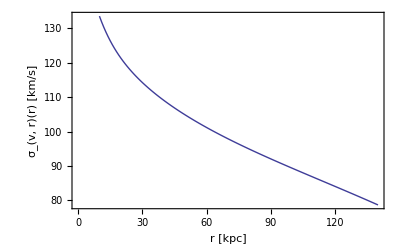

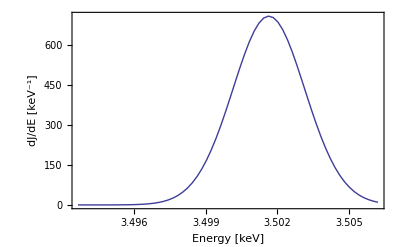

```mathematica
mBH=2.6 10^6;   (* Mass of BH in MW in M_⊙ as given in Klypin, Zhao and Somerville *)
Mb=4.8 10^10;   (* Subscript[M, b]^vir in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rd=3.5;   (* rd in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
MassBaryon[r_]:=mBH+0.025 Mb (1-Exp[-2.64 r^1.15])+0.142 Mb(1-(1+r^1.5)Exp[-r^1.5])+0.833 Mb(1-(1+r/rd)Exp[-r/rd]);   (* Baryonic mass inside radius r from eqn. 11 in Klypin, Zhao and Somerville *)
Conc=12;   (* Concentration for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rvir=258;   (* Virial radius in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rsKlypin=rvir/Conc;   (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mvir=10^12 ;   (* Subscript[M, vir] in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
Mhalo[r_]:=Mvir (Log[1+r/rsKlypin]-(r/rsKlypin)/(1+r/rsKlypin))/(Log[1+Conc]-Conc/(1+Conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rsKlypin)(1+r/rsKlypin)^2 NIntegrate[(MassBaryon[r1]+Mhalo[r1])/(r1^2 (r1/rsKlypin)(1+r1/rsKlypin)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.5](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8.5 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV cm^-3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(45π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(45π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(45π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(45π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,200.}];   (* dJ/dE in keV^-1 --- before convolving with Astro-H resolution at ℓ = 20^0 and b = 5^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 45^0 and b = 25^0 *)
```

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l45degree_b25degree.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 45^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l45degree_b25degree.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl45Degreeb25DegreeTable=Import["dJdE_3point5keV_MicroX_l45degree_b25degree.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 45^0 and b = 25^0 *)    
dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation=Interpolation[dJdE3point5keVMicroXl45Degreeb25DegreeTable,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 45^0 and b = 25^0 *)
```

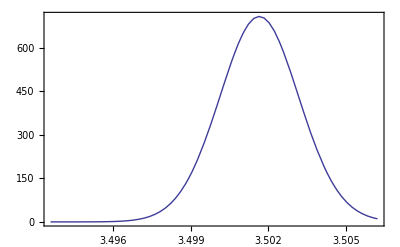

```mathematica
Plot[dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 45^0 and b = 25^0 *)
```

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl45Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 45^0 and b = 25^0 *)
```

0.00154637

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.546^2+1.274^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 45^0 and b = 25^0 *)
```

2.0033

```mathematica
0.001546/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 45^0 and b = 25^0 *)
```

132.514

```mathematica
0.0020033/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 45^0 and b = 25^0 *)
```

171.711

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
Cos[-π/4]
```

1/(√2)

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];   (* Calculating the J factor at (ℓ, b) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
```

2.86548

```mathematica
rs=20;(*Subscript[R,s] as given in the paper by Ng,Horiuchi etal.*)
Rsolar=8;(*Subscript[R,solar]=8 kpc*)
rhosolar=0.4 10^6;(*Subscript[ρ,solar]=0.4 GeV cm^-3=0.4*10^6 keV/cm^3*)
r[ℓ_,b_,s_]:=Sqrt[s^2+Rsolar^2-2 s Rsolar Cos[b] Cos[ℓ]];(*Radial distance r from the Galactic Center in terms of the line of sight distance s,and the Galactic coordinates ℓ and b*)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1 ((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];   (* Calculating the J factor at (ℓ, b) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(25.25 π)/180,(64.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}]   (* ∫ J(ℓ, b) dΩ = Subscript[Σ, ΔΩ] J(ℓ, b) ΔΩ in steps of 0.5 arcminute = 0.5 * 290.89 μrad *)
```

2.86548

1.37927

```mathematica
1.9 10^-2 2.865 1 0.38 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ J dN/dE Subscript[A, eff] ΔΩ T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; J = 2.865; Subscript[A, eff] = 1 cm^2; ΔΩ = 0.38 sr; T = 300 sec  *)
```

6.20559

```mathematica
1.9 10^-2 1 1.379 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.379; T = 300 sec  *)
```

7.8603

```mathematica
1.9 10^-2 1 1.379 π/4 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.379 --- I multiply by the factor π/4 to mimic a circular FoV; T = 300 sec  *)
```

6.17347

```mathematica
R = 1./6.17;
Sqrt[1+4R]
```

1.28386

```mathematica
1.283/Sqrt[6.17] 0.0020033/3.5 3 10^5
```

88.6918

## ℓ = 25^0, b = 25^0

133.599

136.323

-Graphics-

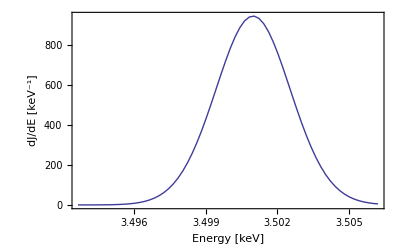

```mathematica
mBH=2.6 10^6;   (* Mass of BH in MW in M_⊙ as given in Klypin, Zhao and Somerville *)
Mb=4.8 10^10;   (* Subscript[M, b]^vir in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rd=3.5;   (* rd in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
MassBaryon[r_]:=mBH+0.025 Mb (1-Exp[-2.64 r^1.15])+0.142 Mb(1-(1+r^1.5)Exp[-r^1.5])+0.833 Mb(1-(1+r/rd)Exp[-r/rd]);   (* Baryonic mass inside radius r from eqn. 11 in Klypin, Zhao and Somerville *)
Conc=12;   (* Concentration for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rvir=258;   (* Virial radius in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rsKlypin=rvir/Conc;   (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mvir=10^12 ;   (* Subscript[M, vir] in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
Mhalo[r_]:=Mvir (Log[1+r/rsKlypin]-(r/rsKlypin)/(1+r/rsKlypin))/(Log[1+Conc]-Conc/(1+Conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rsKlypin)(1+r/rsKlypin)^2 NIntegrate[(MassBaryon[r1]+Mhalo[r1])/(r1^2 (r1/rsKlypin)(1+r1/rsKlypin)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.5](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8.5 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(25π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(25π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,200.}];   (* dJ/dE in keV^-1 --- before convolving with Astro-H resolution at ℓ = 20^0 and b = 5^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 25^0 and b = 25^0 *)
```

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l25degree_b25degree.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l25degree_b25degree.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl25Degreeb25DegreeTable=Import["dJdE_3point5keV_MicroX_l25degree_b25degree.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)    
dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation=Interpolation[dJdE3point5keVMicroXl25Degreeb25DegreeTable,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

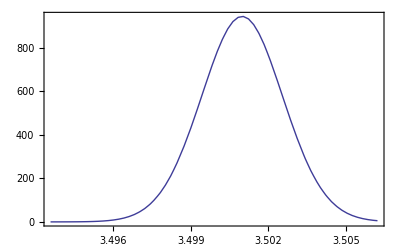

```mathematica
Plot[dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl25Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 25^0 and b = 25^0 *)
```

0.00160055

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.6^2+1.274^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 45^0 and b = 25^0 *)
```

2.04526

```mathematica
0.0016/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 45^0 and b = 25^0 *)
```

137.143

```mathematica
0.002045/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 45^0 and b = 25^0 *)
```

175.286

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
Jfactor[(165 π)/180.,(-5π)/180.]     (* Calculating the J factor at (ℓ = 165^o, b = -5^o) *)
```

2.86548

3.89389

2.4306

1.71702

1.0613

```mathematica
rs=20;(*Subscript[R,s] as given in the paper by Ng,Horiuchi etal.*)
Rsolar=8;(*Subscript[R,solar]=8 kpc*)
rhosolar=0.4 10^6;(*Subscript[ρ,solar]=0.4 GeV cm^-3=0.4*10^6 keV/cm^3*)
r[ℓ_,b_,s_]:=Sqrt[s^2+Rsolar^2-2 s Rsolar Cos[b] Cos[ℓ]];(*Radial distance r from the Galactic Center in terms of the line of sight distance s,and the Galactic coordinates ℓ and b*)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1 ((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];   (* Calculating the J factor at (ℓ, b) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(5.25 π)/180,(44.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}]   (* ∫ J(ℓ, b) dΩ = Subscript[Σ, ΔΩ] J(ℓ, b) ΔΩ in steps of 0.5 arcminute = 0.5 * 290.89 μrad *)
```

3.89389

1.88734

```mathematica
1.9 10^-2 3.89 1 0.38 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ J dN/dE Subscript[A, eff] ΔΩ T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; J = 3.89; Subscript[A, eff] = 1 cm^2; ΔΩ = 0.38 sr; T = 300 sec  *)
```

8.42574

```mathematica
1.9 10^-2  1 1.89 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.89; T = 300 sec  *)
```

10.773

```mathematica
1.9 10^-2  1 1.89 π/4 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.89 --- we multiply by the factor π/4 to mimic a circular FoV; T = 300 sec  *)
```

8.46109

```mathematica
R=1/8.46;
Sqrt[1+4R]
```

1.2136

```mathematica
1.21/Sqrt[8.46] 0.0020033/3.5 3 10^5
```

71.4331

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;
Jfactor[ℓ_,b_]:=(* 1/(Rsolar  rhosolar)  *)NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(45π)/180.,(25π)/180.]
Jfactor[(25π)/180.,(25π)/180.]
ParallelSum[Jfactor[ℓ,b]  9 (290.89 10^-6)^2,{ℓ,(0π)/180.,(40π)/180.,3 290.89 10^-6},{b,(-20π)/180.,(20π)/180.,3 290.89 10^-6}]
```

9.16954×10^6

1.24604×10^7

8.82193×10^6

```mathematica
9.93 0.38
```

3.7734

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8.5;   (* Subscript[R, solar] = 8.5 kpc *)
rhosolar=0.3;   (* Subscript[ρ, solar] = 0.3 GeV cm^-3 = 0.3 × 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]]/Rsolar)^-1((1+(Rsolar/rs))/(1+(Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]]/rs)))^2;
Jfactor[ℓ_,b_]:=(* 1/(Rsolar  rhosolar)  *) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(45π)/180.,(25π)/180.]
Jfactor[(25π)/180.,(25π)/180.]
Jfactor[(20π)/180.,(0π)/180.]
ParallelSum[Jfactor[ℓ,b]  9 (290.89 10^-6)^2,{ℓ,(1.5 π)/180.,(38.5π)/180.,3 290.89 10^-6},{b,(-18.5π)/180.,(18.5π)/180.,3 290.89 10^-6}]
```

7.26052

9.92661

14.685

6.08766

## ℓ = 65^0, b = 25^0

133.599

136.323

-Graphics-

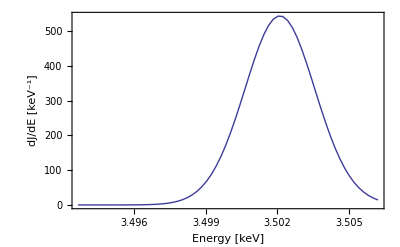

```mathematica
mBH=2.6 10^6;   (* Mass of BH in MW in M_⊙ as given in Klypin, Zhao and Somerville *)
Mb=4.8 10^10;   (* Subscript[M, b]^vir in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rd=3.5;   (* rd in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
MassBaryon[r_]:=mBH+0.025 Mb (1-Exp[-2.64 r^1.15])+0.142 Mb(1-(1+r^1.5)Exp[-r^1.5])+0.833 Mb(1-(1+r/rd)Exp[-r/rd]);   (* Baryonic mass inside radius r from eqn. 11 in Klypin, Zhao and Somerville *)
Conc=12;   (* Concentration for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rvir=258;   (* Virial radius in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rsKlypin=rvir/Conc;   (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mvir=10^12 ;   (* Subscript[M, vir] in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
Mhalo[r_]:=Mvir (Log[1+r/rsKlypin]-(r/rsKlypin)/(1+r/rsKlypin))/(Log[1+Conc]-Conc/(1+Conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rsKlypin)(1+r/rsKlypin)^2 NIntegrate[(MassBaryon[r1]+Mhalo[r1])/(r1^2 (r1/rsKlypin)(1+r1/rsKlypin)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.5](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8.5 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(65π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(65π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,200.}];   (* dJ/dE in keV^-1 --- before convolving with Astro-H resolution at ℓ = 65^0 and b = 25^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 65^0 and b = 25^0 *)
```

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l65degree_b25degree.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l65degree_b25degree.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl65Degreeb25DegreeTable=Import["dJdE_3point5keV_MicroX_l65degree_b25degree.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)    
dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation=Interpolation[dJdE3point5keVMicroXl65Degreeb25DegreeTable,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

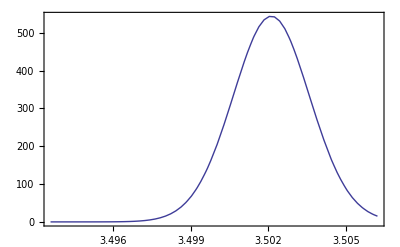

```mathematica
Plot[dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 65^0 and b = 25^0 *)
```

0.00149632

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.496^2+1.274^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 65^0 and b = 25^0 *)
```

1.96497

```mathematica
0.001496/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 65^0 and b = 25^0 *)
```

128.229

```mathematica
0.00196497/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 65^0 and b = 25^0 *)
```

168.426

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
Jfactor[(65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
```

2.86548

3.89389

2.4306

1.71702

2.17403

```mathematica
rs=20;(*Subscript[R,s] as given in the paper by Ng,Horiuchi etal.*)
Rsolar=8;(*Subscript[R,solar]=8 kpc*)
rhosolar=0.4 10^6;(*Subscript[ρ,solar]=0.4 GeV cm^-3=0.4*10^6 keV/cm^3*)
r[ℓ_,b_,s_]:=Sqrt[s^2+Rsolar^2-2 s Rsolar Cos[b] Cos[ℓ]];(*Radial distance r from the Galactic Center in terms of the line of sight distance s,and the Galactic coordinates ℓ and b*)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1 ((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(65π)/180.,(25π)/180.]
ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(45.25 π)/180,(84.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}]
```

2.17403

1.04641

```mathematica
1.9 10^-2 2.17 1 0.38 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ J dN/dE Subscript[A, eff] ΔΩ T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; J = 2.17; Subscript[A, eff] = 1 cm^2; ΔΩ = 0.38 sr; T = 300 sec  *)
```

4.70022

```mathematica
1.9 10^-2  1 1.046 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.046; T = 300 sec  *)
```

5.9622

```mathematica
1.9 10^-2  1 1.046 π/4 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.046 --- I multiply by a factor of π/4 to mimic a circular FoV; T = 300 sec  *)
```

4.6827

```mathematica
R=1/4.68;
Sqrt[1+4R]
```

1.36187

```mathematica
1.36/Sqrt[4.68] 0.00196/3.5 3 10^5
```

105.615

## ℓ = -65^0, b = 25^0

```mathematica
mBH=2.6 10^6;   (* Mass of BH in MW in M_⊙ as given in Klypin, Zhao and Somerville *)
Mb=4.8 10^10;   (* Subscript[M, b]^vir in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rd=3.5;   (* rd in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
MassBaryon[r_]:=mBH+0.025 Mb (1-Exp[-2.64 r^1.15])+0.142 Mb(1-(1+r^1.5)Exp[-r^1.5])+0.833 Mb(1-(1+r/rd)Exp[-r/rd]);   (* Baryonic mass inside radius r from eqn. 11 in Klypin, Zhao and Somerville *)
Conc=12;   (* Concentration for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rvir=258;   (* Virial radius in kpc for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
rsKlypin=rvir/Conc;   (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mvir=10^12 ;   (* Subscript[M, vir] in M_⊙ for Model Subscript[A, 1] as given in Klypin, Zhao and Somerville *)
Mhalo[r_]:=Mvir (Log[1+r/rsKlypin]-(r/rsKlypin)/(1+r/rsKlypin))/(Log[1+Conc]-Conc/(1+Conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rsKlypin)(1+r/rsKlypin)^2 NIntegrate[(MassBaryon[r1]+Mhalo[r1])/(r1^2 (r1/rsKlypin)(1+r1/rsKlypin)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.5](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8.5 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(65π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(65π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,200.}];   (* dJ/dE in keV^-1 --- before convolving with Astro-H resolution at ℓ = 65^0 and b = 25^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 65^0 and b = 25^0 *)
```

133.599

136.323

-Graphics-

-Graphics-

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l65degree_b25degree.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l65degree_b25degree.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl65Degreeb25DegreeTable=Import["dJdE_3point5keV_MicroX_l65degree_b25degree.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)    
dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation=Interpolation[dJdE3point5keVMicroXl65Degreeb25DegreeTable,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

```mathematica
Plot[dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

-Graphics-

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl65Degreeb25DegreeTableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 65^0 and b = 25^0 *)
```

0.00149632

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.496^2+1.274^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 65^0 and b = 25^0 *)
```

1.96497

```mathematica
0.001496/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 65^0 and b = 25^0 *)
```

128.229

```mathematica
0.00196497/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 65^0 and b = 25^0 *)
```

168.426

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[(65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
```

2.17403

2.17403

```mathematica
rs=20;(*Subscript[R,s] as given in the paper by Ng,Horiuchi etal.*)
Rsolar=8;(*Subscript[R,solar]=8 kpc*)
rhosolar=0.4 10^6;(*Subscript[ρ,solar]=0.4 GeV cm^-3=0.4*10^6 keV/cm^3*)
r[ℓ_,b_,s_]:=Sqrt[s^2+Rsolar^2-2 s Rsolar Cos[b] Cos[ℓ]];(*Radial distance r from the Galactic Center in terms of the line of sight distance s,and the Galactic coordinates ℓ and b*)
rhoNFW[ℓ_,b_,s_]:=rhosolar (r[ℓ,b,s]/Rsolar)^-1 ((1+(Rsolar/rs))/(1+(r[ℓ,b,s]/rs)))^2;
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,200.}];
Jfactor[(-65π)/180.,(25π)/180.]
ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(-84.75 π)/180., (-45.25 π)/180,0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}]
```

2.17403

1.0463

```mathematica
1.9 10^-2 2.17 1 0.38 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ J dN/dE Subscript[A, eff] ΔΩ T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; J = 2.17; Subscript[A, eff] = 1 cm^2; ΔΩ = 0.38 sr; T = 300 sec  *)
```

4.70022

```mathematica
1.9 10^-2  1 1.046 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.046; T = 300 sec  *)
```

5.9622

```mathematica
1.9 10^-2  1 1.046 π/4 300   (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.046 --- I multiply by a factor of π/4 to mimic a circular FoV; T = 300 sec  *)
```

4.6827

```mathematica
R=1/4.68;
Sqrt[1+4R]
```

1.36187

```mathematica
1.36/Sqrt[4.68] 0.00196/3.5 3 10^5
```

105.615

## Plot

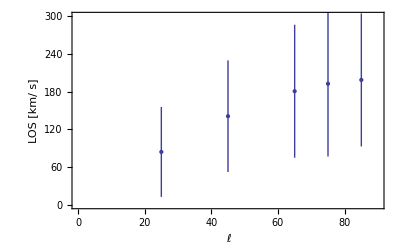

```mathematica
Needs["ErrorBarPlots`"];
ErrorListPlot[{{{25,220 Sin[(25π)/180.] Cos[(25π)/180.]},ErrorBar[71.43]},{{45,220 Sin[(45π)/180.] Cos[(25π)/180.]},ErrorBar[88.69]},{{65,220 Sin[(65π)/180.] Cos[(25π)/180.]},ErrorBar[105.62]},{{75,220 Sin[(75π)/180.] Cos[(25π)/180.]},ErrorBar[115.62]},{{85,220 Sin[(85π)/180.] Cos[(25π)/180.]},ErrorBar[105.62]}},PlotRange->{{0,90},{0,300}},Frame->True,FrameLabel->{"ℓ","LOS [km/ s]"}]
```

## J-factor table

```mathematica
rs=20;   (* Subscript[R, s] as given in the paper by Ng, Horiuchi etal. *)
Rsolar=8;   (* Subscript[R, solar] = 8 kpc *)
rhosolar=0.4 10^6;   (* Subscript[ρ, solar] = 0.4 GeV cm^-3 = 0.4 * 10^6 keV/ cm^3 *)
r[ψ_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[ψ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ψ_,s_]:=rhosolar (r[ψ,s]/Rsolar)^-1((1+(Rsolar/rs))/(1+(r[ψ,s]/rs)))^2;
Jfactor[ψ_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ψ,s],{s,10^-3,200.}];
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["j_table_nfw.dat",ParallelTable[{ψ 180/π,Jfactor[ψ]},{ψ,0.001,π,0.001}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.19375}. NIntegrate obtained 9.3591×10^7 and 1.31491×10^7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.19375}. NIntegrate obtained 8.25892×10^7 and 4.42346×10^6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {8.19375}. NIntegrate obtained 7.71617×10^7 and 1.70523×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

j_table_nfw.dat

# Halo 374

## ℓ = 65^0, b = 25^0

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 10^6;   (* Subscript[ρ, 0] in keV cm^-3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,193.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[(65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(45.25 π)/180,(84.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}]
```

```mathematica
((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)
```

0.260275

```mathematica
((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 1/((8/19.78)(1+8/19.78)^2)
```

0.326255

## ℓ = 25^0, b = 25^0

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)  10^6;   (* Subscript[ρ, 0] in keV/ cm^3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,193.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[(25 π)/180.,(25π)/180.] ;  (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
l25b25=ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(5.25 π)/180,(44.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}];
```

```mathematica
Export["lb.dat",l25b25]
```

lb.dat

## ℓ = 45^0, b = 25^0

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)  10^6;   (* Subscript[ρ, 0] in keV/ cm^3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,193.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[(45 π)/180.,(25π)/180.] ;  (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
l45b25=ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(25.25 π)/180,(64.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}];
```

```mathematica
Export["lb2.dat",l45b25]
```

lb.dat

## ℓ = -65^0, b = 25^0

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)  10^6;   (* Subscript[ρ, 0] in keV/ cm^3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,130.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[-(65 π)/180.,(25π)/180.] ;  (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
lm65b25=ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(-84.75 π)/180,(-45.25 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}];
```

```mathematica
Export["lb3.dat",lm65b25]
```

## ℓ = 25^0, b = 25^0 -- calculation with Halo 374 parameters

116.229

114.604

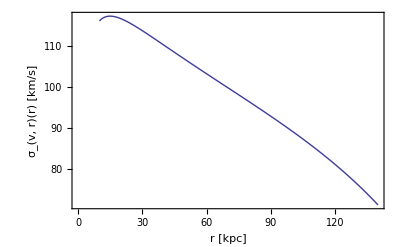

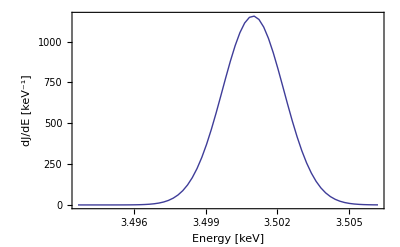

```mathematica
rs=19.78;  (* in kpc *)
Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 10^6;   (* Subscript[ρ, 0] in keV cm^-3 --- we use 10^6 to change from GeV to keV; we use (3.1*10^18 10^3) to change from kpc to cm --- we use (2*10^33) to change from M_⊙ to g --- we use 1.783*10^-24 to change from g to GeV  *)
rhosolar=0.326255 10^6;(* Subscript[ρ, solar] = 0.326255 GeV cm^-3 = 0.326255*10^6 keV/cm^3 *)
Mvir=NIntegrate[4π rintegrand^2  (6912562.96)/((rintegrand/19.78)(1+rintegrand/19.78)^2),{rintegrand,0.01,193.}];
rvir=193.;
conc=rvir/rs;  (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mhalo[r_]:=Mvir (Log[1+r/rs]-(r/rs)/(1+r/rs))/(Log[1+conc]-conc/(1+conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rs)(1+r/rs)^2 NIntegrate[Mhalo[r1]/(r1^2 (r1/rs)(1+r1/rs)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(25π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(25π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(25π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,193.}];   (* dJ/dE in keV^-1 --- before convolving with Micro-X resolution at ℓ = 25^0 and b = 25^0 --- I have only used the values at ℓ = 25^0 and b = 25^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 25^0 and b = 25^0 *)
```

```mathematica
dJdE[3.5]
```

865.692

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l25degree_b25degree_Halo374.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l25degree_b25degree_Halo374.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl25Degreeb25DegreeHalo374Table=Import["dJdE_3point5keV_MicroX_l25degree_b25degree_Halo374.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)    
dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation=Interpolation[dJdE3point5keVMicroXl25Degreeb25DegreeHalo374Table,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

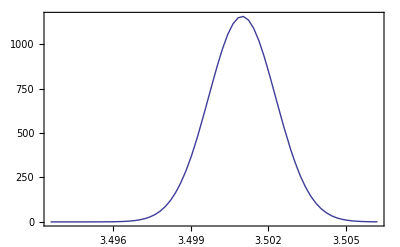

```mathematica
Plot[dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 25^0 and b = 25^0 *)
```

```mathematica
NIntegrate[En dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]/NIntegrate[dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]
```

3.50098

```mathematica
3.5 + (5 220)/(3 10^5) Sin[(25π)/180.] Cos[(25π)/180.]
```

3.5014

```mathematica
220/(3 10^5) Sin[(20π)/180.] Cos[(5π)/180.]
```

0.00024986

```mathematica
0.00098/0.00024986
```

3.9222

```mathematica
0.03/100
```

0.0003

```mathematica
3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])
```

3.50637

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl25Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 25^0 and b = 25^0 *)
```

0.00130177

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.30177^2+1.27398^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 25^0 and b = 25^0 *)
```

1.82144

```mathematica
0.00130177/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 25^0 and b = 25^0 *)
```

111.58

```mathematica
0.00182144/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 25^0 and b = 25^0 *)
```

156.123

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)  10^6;   (* Subscript[ρ, 0] in keV/ cm^3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,193.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[(25 π)/180.,(25π)/180.] ;  (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
l25b25=ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(5.25 π)/180,(44.75 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}];   (* ∫ J(ℓ, b) dΩ = Subscript[Σ, ΔΩ] J(ℓ, b) ΔΩ in steps of 0.5 arcminute = 0.5 * 290.89 μrad *)
```

$Aborted

```mathematica
Export["lb.dat",l25b25]
```

```mathematica
1.9 10^-2  1 1.887 π/4 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.887 --- we multiply by the factor π/4 to mimic a circular FoV; T = 300 sec  *)
```

8.44766

```mathematica
R=1/8.447;
Sqrt[1+4R]
```

1.21389

```mathematica
1.21389/Sqrt[8.447] 0.00182144/3.5 3 10^5
```

65.2073

# Using parameters from Halo 374

ℓ = b = 25^0  -- calculation with Halo 374 parameters

Takes into account varying value of ρ(r) in the calculation of dN/dE

```mathematica
rs=19.78;  (* in kpc *)
Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 10^6;   (* Subscript[ρ, 0] in keV cm^-3 --- we use 10^6 to change from GeV to keV; we use (3.1*10^18 10^3) to change from kpc to cm --- we use (2*10^33) to change from M_⊙ to g --- we use 1.783*10^-24 to change from g to GeV  *)
rhosolar=0.326255 10^6;  (* Subscript[ρ, solar] = 0.326255 GeV cm^-3 = 0.326255*10^6 keV/cm^3 *)
Mvir=NIntegrate[4π rintegrand^2  (6912562.96)/((rintegrand/19.78)(1+rintegrand/19.78)^2),{rintegrand,0.01,193.}];
rvir=193.;
conc=rvir/rs;  (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mhalo[r_]:=Mvir (Log[1+r/rs]-(r/rs)/(1+r/rs))/(Log[1+conc]-conc/(1+conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rs)(1+r/rs)^2 NIntegrate[Mhalo[r1]/(r1^2 (r1/rs)(1+r1/rs)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdEdOmega[ℓ_,b_,En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[ℓ,b,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[ℓ]Cos[b]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[ℓ] Cos[b]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[ℓ]Cos[b]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,193.}];   (* dJ/dE in keV^-1 --- before convolving with Micro-X resolution at ℓ = 25^0 and b = 25^0 *)
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdEdOmega.m",ParallelTable[{En,ℓ,b,dJdEdOmega[ℓ,b,En]},{ℓ,(5.25 π)/180,(44.75 π)/180., 0.0344703},{b,(5.25 π)/180,(44.75 π)/180., 0.0344703},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.00021233}]](* Making a table of dJ/(dE dΩ) over a bin centered around 3.5 keV at ℓ = 25^0 and b = 25^0 *)
```

116.229

114.604

-Graphics-

{«1»}

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdEdOmegaTable=Import["dJdEdOmega.m"];   (* Importing the table of dJ/(dE dΩ) *)
dJdEdOmegaTableFlatten=Flatten[dJdEdOmegaTable,2];   (* Flattening the table of dJ/(dE dΩ) *)
dJdEdOmegaTableFlattenInterpolation=Interpolation[dJdEdOmegaTableFlatten,InterpolationOrder->1]   (* Interpolating the table of dJ/(dE dΩ) *)
```

InterpolatingFunction[{{3.49363,3.50637},{0.0916298,0.746565},{0.0916298,0.746565}},<>]

```mathematica
dJdEdOmegaTableFlattenInterpolation[3.50573,0.78103,0.78103]   (* Using the interpolating function to find the value of dJ/(dE dΩ) in a specific energy, and ℓ and b *)
```

2.66412

```mathematica
dJdETable=ParallelTable[{En,π/4 0.0344703^2  ParallelSum[dJdEdOmegaTableFlattenInterpolation[En,ℓ,b],{ℓ,(5.25 π)/180,(44.75 π)/180.,0.0344703},{b,(5.25 π)/180,(44.75 π)/180., 0.0344703}]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.00021233}]   (* Finding the expressin of dJ/dE by integrating of the solid angle --- we use a factor of π/4 to convert the FoV from a sqaure to a circle *)
```

{{3.49363,0.000282015},{3.49384,0.000630819},{3.49405,0.00137995},{3.49427,0.00295213},{3.49448,0.00617604},{3.49469,0.0126349},{3.4949,0.0252754},{3.49512,0.0494389},{3.49533,0.0945481},{3.49554,0.176774},{3.49575,0.323091},{3.49597,0.577204},{3.49618,1.00781},{3.49639,1.71955},{3.4966,2.86661},{3.49682,4.66837},{3.49703,7.42539},{3.49724,11.5329},{3.49745,17.4872},{3.49766,25.8797},{3.49788,37.3717},{3.49809,52.6451},{3.4983,72.3257},{3.49851,96.8815},{3.49873,126.504},{3.49894,160.992},{3.49915,199.649},{3.49936,241.243},{3.49958,284.014},{3.49979,325.779},{3.5,364.098},{3.50021,396.513},{3.50042,420.813},{3.50064,435.3},{3.50085,438.987},{3.50106,431.707},{3.50127,414.114},{3.50149,387.586},{3.5017,354.051},{3.50191,315.759},{3.50212,275.023},{3.50234,234.001},{3.50255,194.529},{3.50276,158.029},{3.50297,125.464},{3.50318,97.357},{3.5034,73.8418},{3.50361,54.7439},{3.50382,39.6707},{3.50403,28.0997},{3.50425,19.4546},{3.50446,13.165},{3.50467,8.70715},{3.50488,5.62836},{3.5051,3.55562},{3.50531,2.19514},{3.50552,1.32436},{3.50573,0.780798},{3.50595,0.449825},{3.50616,0.253229},{3.50637,0.139297}}

```mathematica
dJdETableInterpolation=Interpolation[dJdETable,InterpolationOrder->1]   (* Interpolating the above table *)
```

InterpolatingFunction[{{3.49363,3.50637}},<>]

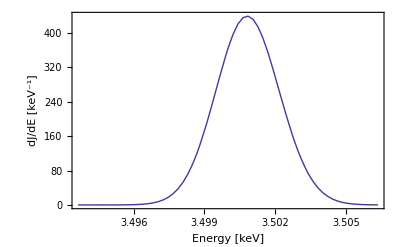

```mathematica
Plot[dJdETableInterpolation[En],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])},Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]  (* Plotting the function *)
```

```mathematica
fit=FindFit[{{3.49363008649784,0.00028201512444444617},{3.49384241649784,0.0006308187938799722},{3.49405474649784,0.001379945785677341},{3.49426707649784,0.0029521251423522757},{3.49447940649784,0.006176037345287689},{3.49469173649784,0.01263488290608004},{3.49490406649784,0.025275445192249234},{3.4951163964978402,0.04943889184382558},{3.4953287264978403,0.09454813921888094},{3.49554105649784,0.17677385932217962},{3.49575338649784,0.3230912729237084},{3.49596571649784,0.5772043141501103},{3.4961780464978403,1.007811300761464},{3.4963903764978403,1.7195500194348736},{3.49660270649784,2.866611495368476},{3.49681503649784,4.668369957159529},{3.49702736649784,7.42539199520674},{3.4972396964978403,11.532887234014991},{3.4974520264978404,17.487204559792996},{3.49766435649784,25.879696921273283},{3.49787668649784,37.37169653934469},{3.49808901649784,52.64509740413499},{3.4983013464978403,72.32572220219544},{3.4985136764978404,96.8815205439375},{3.49872600649784,126.50436048656276},{3.49893833649784,160.9915530979493},{3.4991506664978402,199.6493330584694},{3.4993629964978403,241.24291016788047},{3.4995753264978404,284.0142589357688},{3.49978765649784,325.7787635763527},{3.49999998649784,364.0978848286339},{3.50021231649784,396.51279657142123},{3.50042464649784,420.8132241815734},{3.50063697649784,435.2997298977969},{3.5008493064978397,438.98662943227487},{3.5010616364978397,431.7073165463021},{3.50127396649784,414.11436438739946},{3.50148629649784,387.5858178679128},{3.50169862649784,354.0514451234702},{3.5019109564978397,315.7592854960513},{3.5021232864978398,275.0232391204621},{3.50233561649784,234.00054657300166},{3.50254794649784,194.52892618989873},{3.50276027649784,158.02858896781422},{3.5029726064978397,125.46390942849088},{3.50318493649784,97.35700852158143},{3.50339726649784,73.84182811907363},{3.50360959649784,54.74391209991476},{3.50382192649784,39.67065012838426},{3.5040342564978397,28.099735578908255},{3.50424658649784,19.4546196057944},{3.50445891649784,13.164958872571479},{3.50467124649784,8.707149796785835},{3.50488357649784,5.628358489255001},{3.5050959064978398,3.555617732012431},{3.50530823649784,2.195138595949128},{3.50552056649784,1.3243647255085687},{3.50573289649784,0.7807981047224222},{3.50594522649784,0.44982538624665547},{3.5061575564978398,0.2532292564712682},{3.50636988649784,0.1392968934469779}},a Exp[(- (t-t0)^2)/(2 σ^2)],{{a,500},{t0,3.5},{σ,0.00135}},t]   (* Trying to fit a function to dJ/dE *)
```

{a→438.62,t0→3.50083,σ→0.00134421}

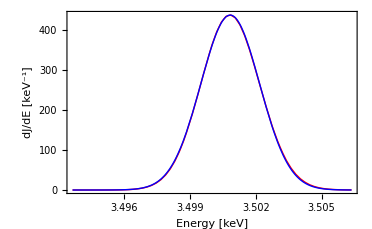

```mathematica
Plot[{dJdETableInterpolation[En],438.62 Exp[-1/2 (En-3.50083)^2/(0.001344321)^2]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])},Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"},PlotStyle->{Red,Blue}]   (* Comparing the fit to the actual line shape *)
```

```mathematica
3.5 -  3 10^-3 3 1/(2 Sqrt[2 Log[2]])
```

3.49618

```mathematica
3.5 + 3 10^-3 3 1/(2 Sqrt[2 Log[2]])
```

3.50382

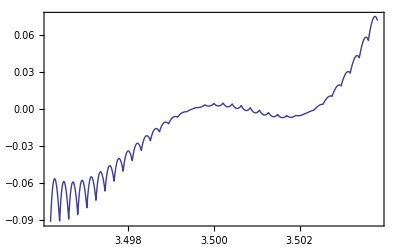

```mathematica
Plot[{(dJdETableInterpolation[En]-438.62Exp[-1/2 (En-3.50083)^2/(0.00134421)^2])/dJdETableInterpolation[En]},{En,3.5 -  3 10^-3 3 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 3 1/(2 Sqrt[2 Log[2]])},Frame->True]   (* Comparing the error in the fit *)
```

```mathematica
3.5(1+220/(3. 10^5) Sin[(20 π)/180.] Cos[(19 π)/180])
```

3.50083

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ 438.62   Exp[-1/2 (En1-3.50083)^2/(0.00134421)^2],{En1,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}] En^2 438.62Exp[-1/2 (En-3.50083)^2/(0.00134421)^2],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}]- (1/NIntegrate[438.62  Exp[-1/2 (En2-3.50083)^2/(0.00134421)^2],{En2,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}] NIntegrate[En 438.62Exp[-1/2 (En-3.50083)^2/(0.00134421)^2],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 25^0 and b = 25^0 *)
```

0.00134398

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.34398^2+1.27398^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 25^0 and b = 25^0 *)
```

1.85184

```mathematica
0.00134398/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 25^0 and b = 25^0 *)
```

115.198

```mathematica
0.00185184/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 25^0 and b = 25^0 *)
```

158.729

```mathematica
1.9 10^-2  1 1.887 π/4 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.887 --- we multiply by the factor π/4 to mimic a circular FoV; T = 300 sec --- we calculate ∫ J(ℓ, b) dΩ = 1.887 in lb.dat *)
```

8.44766

```mathematica
R=1/8.44766;
Sqrt[1+4R]
```

1.21388

```mathematica
1.21388/Sqrt[8.44766] 0.00185184/3.5 3 10^5
```

66.2925

## ℓ = 65^0, b = 25^0 -- calculation with Halo 374 parameters

For a constant value of ρ in the calculation of dN/dE

116.229

114.604

-Graphics-

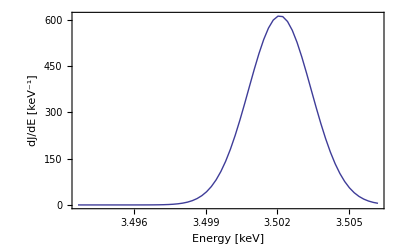

```mathematica
rs=19.78;  (* in kpc *)
Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 10^6;   (* Subscript[ρ, 0] in keV cm^-3 --- we use 10^6 to change from GeV to keV; we use (3.1*10^18 10^3) to change from kpc to cm --- we use (2*10^33) to change from M_⊙ to g --- we use 1.783*10^-24 to change from g to GeV  *)
rhosolar=0.326255 10^6;(* Subscript[ρ, solar] = 0.326255 GeV cm^-3 = 0.326255*10^6 keV/cm^3 *)
Mvir=NIntegrate[4π rintegrand^2  (6912562.96)/((rintegrand/19.78)(1+rintegrand/19.78)^2),{rintegrand,0.01,193.}];
rvir=193.;
conc=rvir/rs;  (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mhalo[r_]:=Mvir (Log[1+r/rs]-(r/rs)/(1+r/rs))/(Log[1+conc]-conc/(1+conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rs)(1+r/rs)^2 NIntegrate[Mhalo[r1]/(r1^2 (r1/rs)(1+r1/rs)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdE[En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[(65π)/180.,(25π)/180.,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[(65π)/180.] Cos[(25π)/180.]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[(65π)/180.]Cos[(25π)/180.]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,193.}];   (* dJ/dE in keV^-1 --- constant ρ --- before convolving with Micr0-X resolution at ℓ = 65^0 and b = 25^0 *)
ListPlot[ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}],Joined->True,Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting dJ/dE over a bin centered around 3.5 keV at ℓ = 65^0 and b = 25^0 --- note that I have kept the density to be constant in the dJ/dE *)
```

```mathematica
dJdE[3.5]
```

174.141

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdE_3point5keV_MicroX_l65degree_b25degree_Halo374.dat",ParallelTable[{En,dJdE[En]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.0002}]]   (* Making a table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

dJdE_3point5keV_MicroX_l65degree_b25degree_Halo374.dat

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdE3point5keVMicroXl65Degreeb25DegreeHalo374Table=Import["dJdE_3point5keV_MicroX_l65degree_b25degree_Halo374.dat"];   (* Importing the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)    
dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation=Interpolation[dJdE3point5keVMicroXl65Degreeb25DegreeHalo374Table,InterpolationOrder->1];   (* Interpolating the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

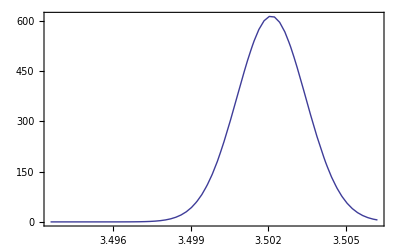

```mathematica
Plot[dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062},Frame->True]   (* Plotting the interpolation of the table of dJ/dE over a bin centered around 3.5 keV and then exporting it at ℓ = 65^0 and b = 25^0 *)
```

```mathematica
NIntegrate[En dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]/NIntegrate[dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]
```

3.5021

```mathematica
220/(3. 10^5) Sin[(65π)/180.] Cos[(25π)/180.]
```

0.000602355

```mathematica
0.0021/0.000602355
```

3.48632

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En1],{En1,3.4936,3.5062}] En^2 dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}]- (1/NIntegrate[dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En2],{En2,3.4936,3.5062}] NIntegrate[En dJdE3point5keVMicroXl65Degreeb25DegreeHalo374TableInterpolation[En],{En,3.4936,3.5062}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 65^0 and b = 25^0 *)
```

0.00132876

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.32876^2+1.27398^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 65^0 and b = 25^0 *)
```

1.84082

```mathematica
0.00132876/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 65^0 and b = 25^0 *)
```

113.894

```mathematica
0.00184082/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 65^0 and b = 25^0 *)
```

157.785

```mathematica
rs=19.78;  (* in kpc *)
 Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3)  10^6;   (* Subscript[ρ, 0] in keV/ cm^3 *)
rhosolar=0.326255 10^6;(*Subscript[ρ,solar]=0.326255 GeV cm^-3 =0.326255*10^6 keV/cm^3 *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1+r[ℓ,b,s]/rs)^-2;   (* Expression for Subscript[ρ, NFW] *)
Jfactor[ℓ_,b_]:=1/(Rsolar  rhosolar) NIntegrate[rhoNFW[ℓ,b,s],{s,10^-3,130.}];
(* Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.]   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *) *)
Jfactor[-(65 π)/180.,(25π)/180.] ;  (* Calculating the J factor at (ℓ = 65^o, b = 25^o) *)
(* Jfactor[(-65 π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = -65^o, b = 25^o) *)
Jfactor[(45π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 25^o) *)
Jfactor[(25π)/180.,(25π)/180.]   (* Calculating the J factor at (ℓ = 25^o, b = 25^o) *)
Jfactor[(45π)/180.,(45π)/180.]   (* Calculating the J factor at (ℓ = 45^o, b = 45^o) *)
Jfactor[(75 π)/180.,(75π)/180.] *)   (* Calculating the J factor at (ℓ = 75^o, b = 75^o) *)
lm65b25=ParallelSum[Jfactor[ℓ,b] (0.5 290.89 10^-6)^2,{ℓ,(-84.75 π)/180,(-45.25 π)/180., 0.5 290.89 10^-6},{b,(5.25 π)/180.,(44.75 π)/180.,0.5 290.89 10^-6}];
```

```mathematica
Export["lb3.dat",lm65b25]
```

```mathematica
1.9 10^-2  1 1.039 π/4 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.039 --- we multiply by the factor π/4 to mimic a circular FoV; T = 300 sec --- we calculate ∫ J(ℓ, b) dΩ = 1.039 in lb3.dat *)
```

4.65136

```mathematica
R=1/4.65136;
Sqrt[1+4R]
```

1.3638

```mathematica
1.3638/Sqrt[4.65136] 0.00184082/3.5 3 10^5   (* Note that this is not correct as we have taken the value of the density profile at ℓ = 65^0, and b = 25^0 to find dN/dE --- the correct thing is done below *)
```

99.7758

Takes into account varying value of ρ in the calculation of dN/dE

```mathematica
rs=19.78;  (* in kpc *)
Rsolar=8;  (* Subscript[R, solar] = 8 kpc *)
rho0=((6912562.96 2 10^33)/(1.783 10^-24) (3.1 10^18 10^3)^-3) 10^6;   (* Subscript[ρ, 0] in keV cm^-3 --- we use 10^6 to change from GeV to keV; we use (3.1*10^18 10^3) to change from kpc to cm --- we use (2*10^33) to change from M_⊙ to g --- we use 1.783*10^-24 to change from g to GeV  *)
rhosolar=0.326255 10^6;(* Subscript[ρ, solar] = 0.326255 GeV cm^-3 = 0.326255*10^6 keV/cm^3 *)
Mvir=NIntegrate[4π rintegrand^2  (6912562.96)/((rintegrand/19.78)(1+rintegrand/19.78)^2),{rintegrand,0.01,193.}];
rvir=193.;
conc=rvir/rs;  (* Subscript[r, s] = Subscript[r, vir]/C *)
GN= 6.674 10^-11;   (* Subscript[G, N] in SI units *)
Mhalo[r_]:=Mvir (Log[1+r/rs]-(r/rs)/(1+r/rs))/(Log[1+conc]-conc/(1+conc));   (* Mass of the halo in M_⊙ at a radius r *)
sigmavrsquaredDividedByGN[r_]:= (r/rs)(1+r/rs)^2 NIntegrate[Mhalo[r1]/(r1^2 (r1/rs)(1+r1/rs)^2),{r1,r,rvir}];   (* Formula for (Subscript[σ, v,r]^2(r))/Subscript[G, N] in units of (M_⊙)/kpc as given in DVS paper *)
Sqrt[GN sigmavrsquaredDividedByGN[10](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 10 kpc *)
Sqrt[GN  sigmavrsquaredDividedByGN[8.](2 10^30)/(10^3 3.1 10^16)]/1000.   (* Subscript[σ, v,r](r) in km/s at 8 kpc *)
ListPlot[ParallelTable[{r2,Sqrt[GN  sigmavrsquaredDividedByGN[r2] (2 10^30)/(10^3 3.1 10^16)]/1000.},{r2,10 ,140,1}],Joined->True,Frame->True,FrameLabel->{"r [kpc]","σ_(v, r)(r) [km/s]"}]   (* Plotting Subscript[σ, v,r](r) in km/s *)
r[ℓ_,b_,s_]:=Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[b]Cos[ℓ]];   (* Radial distance r from the Galactic Center in terms of the line of sight distance s, and the Galactic coordinates ℓ and b *)
rhoNFW[ℓ_,b_,s_]:=rho0 (r[ℓ,b,s]/rs)^-1(1/(1+(r[ℓ,b,s]/rs)))^2;   (* Subscript[ρ, NFW] *)
Egamma=3.5;   (* Energy of the monoenergetic photon in keV *)
dJdEdOmega[ℓ_,b_,En_]:=1/(Rsolar  rhosolar)  NIntegrate[rhoNFW[ℓ,b,s]  1/(Sqrt[2π] Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[ℓ]Cos[b]]] (2 10^30)/(10^3 3.1 10^16)]/1000.) Exp[-1/2 ((En-Egamma/(3 10^5) 220 Sin[ℓ] Cos[b]-Egamma)^2)/(( Egamma/(3 10^5) Sqrt[GN  sigmavrsquaredDividedByGN[Sqrt[s^2 + Rsolar^2 - 2 s Rsolar Cos[ℓ]Cos[b]]] (2 10^30)/(10^3 3.1 10^16)]/1000.)^2)],{s,1.,193.}];   (* dJ/dE in keV^-1 --- before convolving with Micro-X resolution at ℓ = 65^0 and b = 25^0 *)
(* SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"]; *)
SetDirectory["/Users/ranjan_laha/Desktop/Doppler_effect_indirect_detection_using_simulations"];
Export["dJdEdOmegal65b25.m",ParallelTable[{En,ℓ,b,dJdEdOmega[ℓ,b,En]},{ℓ,(45.25 π)/180,(84.75 π)/180., 0.0344703},{b,(5.25 π)/180,(44.75 π)/180., 0.0344703},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.00021233}]](* Making a table of dJ/(dE dΩ) over a bin centered around 3.5 keV at ℓ = 65^0 and b = 25^0 *)
```

116.229

114.604

-Graphics-

dJdEdOmegal65b25.m

```mathematica
SetDirectory["/Users/ranjanlaha/Desktop/Desktop/Doppler_effect_indirect_detection_using_simulations"];
dJdEdOmegal65b25Table=Import["dJdEdOmegal65b25.m"];   (* Importing the table of dJ/(dE dΩ) *)
dJdEdOmegal65b25TableFlatten=Flatten[dJdEdOmegal65b25Table,2];   (* Flattening the table of dJ/(dE dΩ) *)
dJdEdOmegal65b25TableFlattenInterpolation=Interpolation[dJdEdOmegal65b25TableFlatten,InterpolationOrder->1]   (* Interpolating the table of dJ/(dE dΩ) *)
```

InterpolatingFunction[{{3.49363,3.50637},{0.789761,1.4447},{0.0916298,0.746565}},<>]

```mathematica
dJdEdOmegal65b25TableFlattenInterpolation[3.50573,0.78103,0.78103](* Using the interpolating function to find the value of dJ/(dE dΩ) in a specific energy, and ℓ and b *)
```

2.67451

```mathematica
dJdEl65b25Table=ParallelTable[{En,π/4 0.0344703^2  ParallelSum[dJdEdOmegal65b25TableFlattenInterpolation[En,ℓ,b],{ℓ,(45.25 π)/180,(84.75 π)/180., 0.0344703},{b,(5.25 π)/180,(44.75 π)/180., 0.0344703}]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),0.00021233}]   (* Finding the expressin of dJ/dE by integrating of the solid angle --- we use a factor of π/4 to convert the FoV from a sqaure to a circle *)
```

{{3.49363,1.69053×10^-6},{3.49384,4.29148×10^-6},{3.49405,0.0000106415},{3.49427,0.0000257747},{3.49448,0.0000609776},{3.49469,0.000140903},{3.4949,0.000318003},{3.49512,0.000700957},{3.49533,0.001509},{3.49554,0.00317258},{3.49575,0.00651406},{3.49597,0.0130616},{3.49618,0.025576},{3.49639,0.0489052},{3.4966,0.0913172},{3.49682,0.166501},{3.49703,0.296441},{3.49724,0.51536},{3.49745,0.874834},{3.49766,1.45003},{3.49788,2.34671},{3.49809,3.70821},{3.4983,5.72121},{3.49851,8.61837},{3.49873,12.6756},{3.49894,18.2019},{3.49915,25.5189},{3.49936,34.9299},{3.49958,46.6787},{3.49979,60.9001},{3.5,77.569},{3.50021,96.4537},{3.50042,117.085},{3.50064,138.746},{3.50085,160.495},{3.50106,181.22},{3.50127,199.72},{3.50149,214.805},{3.5017,225.413},{3.50191,230.732},{3.50212,230.313},{3.50234,224.178},{3.50255,212.807},{3.50276,197.084},{3.50297,178.137},{3.50318,157.166},{3.5034,135.362},{3.50361,113.813},{3.50382,93.427},{3.50403,74.8782},{3.50425,58.5951},{3.50446,44.7721},{3.50467,33.4048},{3.50488,24.3378},{3.5051,17.3155},{3.50531,12.0304},{3.50552,8.16261},{3.50573,5.40865},{3.50595,3.5},{3.50616,2.21194},{3.50637,1.36525}}

```mathematica
dJdEl65b25TableInterpolation=Interpolation[dJdEl65b25Table,InterpolationOrder->1]   (* Interpolating the above table *)
```

InterpolatingFunction[{{3.49363,3.50637}},<>]

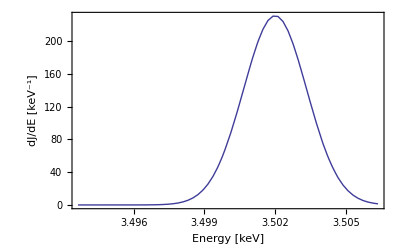

```mathematica
Plot[dJdEl65b25TableInterpolation[En],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])},Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"}]   (* Plotting the function *)
```

```mathematica
fit=FindFit[{{3.49363008649784,1.6905325113458961*^-6},{3.49384241649784,4.291484678839076*^-6},{3.49405474649784,0.000010641467447755871},{3.49426707649784,0.000025774669567392312},{3.49447940649784,0.00006097755983541582},{3.49469173649784,0.00014090295776298599},{3.49490406649784,0.00031800300571289015},{3.4951163964978402,0.000700957172938722},{3.4953287264978403,0.0015089999632617783},{3.49554105649784,0.0031725837345091693},{3.49575338649784,0.0065140644609910595},{3.49596571649784,0.013061572472433608},{3.4961780464978403,0.025576028841670522},{3.4963903764978403,0.04890522191259561},{3.49660270649784,0.09131719093398687},{3.49681503649784,0.1665007739131331},{3.49702736649784,0.2964408813736384},{3.4972396964978403,0.5153595103048335},{3.4974520264978404,0.874833863499064},{3.49766435649784,1.4500295490117152},{3.49787668649784,2.346706253119259},{3.49808901649784,3.708209716033753},{3.4983013464978403,5.7212144592096905},{3.4985136764978404,8.618370867884966},{3.49872600649784,12.67563982342863},{3.49893833649784,18.201917262170493},{3.4991506664978402,25.518876238583307},{3.4993629964978403,34.929907356266035},{3.4995753264978404,46.678683320599006},{3.49978765649784,60.9001117777023},{3.49999998649784,77.56896050268004},{3.50021231649784,96.45373255547668},{3.50042464649784,117.08480621060187},{3.50063697649784,138.74580550093265},{3.5008493064978397,160.49514690262544},{3.5010616364978397,181.2201918743449},{3.50127396649784,199.71955892557168},{3.50148629649784,214.80452544171703},{3.50169862649784,225.41339762509443},{3.5019109564978397,230.73174341587742},{3.5021232864978398,230.31333463214318},{3.50233561649784,224.17800637996842},{3.50254794649784,212.8066918083779},{3.50276027649784,197.08416748646516},{3.5029726064978397,178.1371310779308},{3.50318493649784,157.16614517246109},{3.50339726649784,135.36193137348724},{3.50360959649784,113.81331810739768},{3.50382192649784,93.42695213020488},{3.5040342564978397,74.87815519733145},{3.50424658649784,58.595077893286025},{3.50445891649784,44.77209407558205},{3.50467124649784,33.40483858324554},{3.50488357649784,24.33777318660074},{3.5050959064978398,17.31546299202206},{3.50530823649784,12.03040301803801},{3.50552056649784,8.162606296363109},{3.50573289649784,5.408649999271363},{3.50594522649784,3.500000217392901},{3.5061575564978398,2.211940296597641},{3.50636988649784,1.365246576095123}},a Exp[(- (t-t0)^2)/(2 σ^2)],{{a,500},{t0,3.5},{σ,0.00135}},t]   (* Trying to fit a function to dJ/dE *)
```

{a→230.79,t0→3.502,σ→0.0013551}

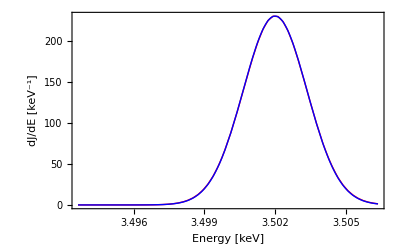

```mathematica
Plot[{dJdEl65b25TableInterpolation[En],230.79Exp[-1/2 (En-3.502)^2/(0.0013551)^2]},{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])},Frame->True,FrameLabel->{"Energy [keV]","dJ/dE [keV^-1]"},PlotStyle->{Red,Blue}]   (* Comparing the fit to the actual line shape *)
```

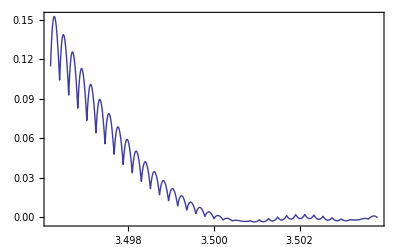

```mathematica
Plot[{(dJdEl65b25TableInterpolation[En]-230.79 Exp[-1/2 (En-3.502)^2/(0.0013551)^2])/dJdEl65b25TableInterpolation[En]},{En,3.5 -  3 10^-3 3 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 3 1/(2 Sqrt[2 Log[2]])},Frame->True]   (* Comparing the error in the fit *)
```

```mathematica
Sqrt[NIntegrate[1/NIntegrate[ 230.79Exp[-1/2 (En1-3.502)^2/(0.0013551)^2],{En1,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}] En^2 230.79Exp[-1/2 (En-3.502)^2/(0.0013551)^2],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}]- (1/NIntegrate[230.79Exp[-1/2 (En2-3.502)^2/(0.0013551)^2],{En2,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}] NIntegrate[En 230.79Exp[-1/2 (En-3.502)^2/(0.0013551)^2],{En,3.5 -  3 10^-3 5 1/(2 Sqrt[2 Log[2]]),3.5 +  3 10^-3 5 1/(2 Sqrt[2 Log[2]])}])^2]   (* Finding the Subscript[σ, DM] in keV of the distribution dJ/dE by calculating <E^2> - <E>^2 at ℓ = 65^0 and b = 25^0 *)
```

0.00135027

```mathematica
3 10^-3 1/(2. Sqrt[2 Log[2]])   (* (3 eV)/(2 √(2 Ln 2)) *)
```

0.00127398

```mathematica
Sqrt[1.35027^2+1.27398^2]   (* Subscript[σ, eff] = √(Subscript[σ, AH]^2 + Subscript[σ, DM]^2) where Subscript[σ, DM] is found in the above line at ℓ = 65^0 and b = 25^0 *)
```

1.85641

```mathematica
0.00135037/3.5 3 10^5  (* Velocity corresponding to Subscript[σ, DM] at ℓ = 65^0 and b = 25^0 *)
```

115.746

```mathematica
0.00185641/3.5 3 10^5   (* Velocity corresponding to Subscript[σ, eff] at ℓ = 65^0 and b = 25^0 *)
```

159.121

```mathematica
1.9 10^-2  1 1.039 π/4 300    (* No. of events = Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙  dN/dE Subscript[A, eff] (∫ J(ℓ, b) dΩ) T --- see page 7 of notes --- here I take Micro-X parameters: Γ/(4π Subscript[m, χ]) R_⊙ ρ_⊙ = 1.9 * 10^-2; Subscript[A, eff] = 1 cm^2; ∫ J(ℓ, b) dΩ = 1.039 --- we multiply by the factor π/4 to mimic a circular FoV; T = 300 sec --- we calculate ∫ J(ℓ, b) dΩ = 1.039 in lb3.dat *)
```

4.65136

```mathematica
R=1/4.65136;
Sqrt[1+4R]
```

1.3638

```mathematica
1.3638/Sqrt[4.65136] 0.00185641/3.5 3 10^5
```

100.621

## Plot

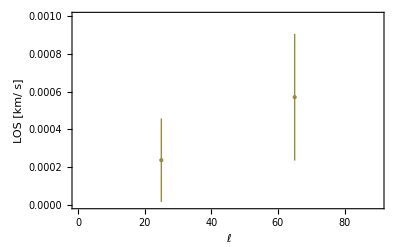

```mathematica
Needs["ErrorBarPlots`"];
ErrorListPlot[{{{25,(3.5 220/(3 10^5) Sin[(20π)/180.] Cos[(19π)/180.])/3.5},ErrorBar[66.2925/(3 10^5)]},,{{65,(3.5 220/(3 10^5) Sin[(64π)/180.] Cos[(30π)/180.])/3.5},ErrorBar[100.621/(3 10^5)]}},PlotRange->{{0,90},{0,10^-3}},Frame->True,FrameLabel->{"ℓ","LOS [km/ s]"}]
```